# QED calculation: Peskin Sec. 5

## e^-e^+→γ γ : Peskin P.153-54

-Graphics-

### Initialization

```mathematica
Exit[];
```

```mathematica
$Language="English";
```

```mathematica
<<FeynArts`
<<FormCalc`
```

FeynArts 3.10 (12 Mar 2018)

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

FormCalc 9.6 (16 Apr 2018)

by Thomas Hahn

### Create Topology & Insert Particles

loading generic model file /Users/misho/.ghq/github.com/HEPcodes/FeynArts/Models/Lorentz.gen

> $GenericMixing is OFF

generic model {Lorentz} initialized

loading classes model file /Users/misho/.ghq/github.com/HEPcodes/FeynArts/Models/SM.mod

$CKM=False

> 46 particles (incl. antiparticles) in 16 classes

> $CounterTerms are ON

> 88 vertices

> 115 counterterms of order 1

> 6 counterterms of order 2

classes model {SM} initialized

inserting at level(s) {Classes}

> Top. 1: 0 Classes insertions

> Top. 2: 0 Classes insertions

> Top. 3: 1 Classes insertion

> Top. 4: 1 Classes insertion

in total: 2 Classes insertions

> Top. 1 aebf/cedf/ef.m, 1 diagram

> Top. 2 aebf/cfde/ef.m, 1 diagram

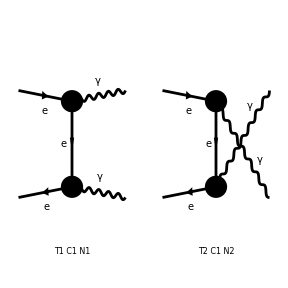

```mathematica
topologies=CreateTopologies[0,2->2];
diagrams=InsertFields[topologies,{F[2,{1}],-F[2,{1}]}->{V[1],V[1]},InsertionLevel->{Classes}];
Paint[diagrams];
```

### Pass the diagram to FormCalc

```mathematica
ClearProcess[];
amplitude=CalcFeynAmp[CreateFeynAmp[diagrams],FermionChains->VA]
```

creating amplitudes at level(s) {Classes}

> Top. 1: 1 Classes amplitude

> Top. 2: 1 Classes amplitude

in total: 2 Classes amplitudes

preparing FORM code in /Users/misho/fc-amp-1.frm

running FORM...

ok

Amp[{{F[2,{1}],k[1],ME,{-Charge,LeptonNumber}},{-F[2,{1}],k[2],ME,{Charge,-LeptonNumber}}}→{{V[1],k[3],0,{}},{V[1],k[4],0,{}}}][-4 Alfa π (Den[T,ME2]+Den[U,ME2]) Mat[F1]+Alfa Pair2 π (4 Den[T,ME2]-4 Den[U,ME2]) Mat[F2]-Alfa Pair1 π (4 Den[T,ME2]-4 Den[U,ME2]) Mat[F3]-Alfa π (8 Pair3 Den[T,ME2]-8 Pair4 Den[U,ME2]) Mat[F4]]

Take an average for initial fermions

```mathematica
_Hel=0;
squared=SquaredME[amplitude]
helSquared=squared//.HelicityME[amplitude]
```

{FF[F1] (FFC[F1] Mat[F1,F1]+FFC[F2] Mat[F1,F2]+FFC[F3] Mat[F1,F3]+FFC[F4] Mat[F1,F4])+FF[F2] (FFC[F1] Mat[F2,F1]+FFC[F2] Mat[F2,F2]+FFC[F3] Mat[F2,F3]+FFC[F4] Mat[F2,F4])+FF[F3] (FFC[F1] Mat[F3,F1]+FFC[F2] Mat[F3,F2]+FFC[F3] Mat[F3,F3]+FFC[F4] Mat[F3,F4])+FF[F4] (FFC[F1] Mat[F4,F1]+FFC[F2] Mat[F4,F2]+FFC[F3] Mat[F4,F3]+FFC[F4] Mat[F4,F4]),{FF[F1]→-4 Alfa π (Den[T,ME2]+Den[U,ME2]),FF[F2]→Alfa Pair2 π (4 Den[T,ME2]-4 Den[U,ME2]),FF[F3]→-Alfa Pair1 π (4 Den[T,ME2]-4 Den[U,ME2]),FF[F4]→-Alfa π (8 Pair3 Den[T,ME2]-8 Pair4 Den[U,ME2]),FFC[F1]→-4 Alfa π (Den[T,ME2]+Den[U,ME2]),FFC[F2]→Alfa π Pair2^* (4 Den[T,ME2]-4 Den[U,ME2]),FFC[F3]→-Alfa π Pair1^* (4 Den[T,ME2]-4 Den[U,ME2]),FFC[F4]→-Alfa π (8 Pair3^* Den[T,ME2]-8 Pair4^* Den[U,ME2])}}

> 16 helicity matrix elements

preparing FORM code in /Users/misho/fc-hel-1.frm

running FORM...

ok

{FF[F1] (1/2 (-Abb9-2 ME2 Pair2 Pair8) FFC[F1]-1/2 Abb3 FFC[F2]-1/2 Abb1 Pair2 FFC[F3]-1/2 Abb5 FFC[F4])+FF[F4] (1/2 Abb22 FFC[F1]+1/2 (-Abb18-2 ME2 Pair7) FFC[F2]+1/2 (-Abb20-2 ME2 Pair2) FFC[F3]+1/2 (Abb19+2 ME2) FFC[F4])+FF[F3] (-1/2 Abb13 Pair8 FFC[F1]-1/2 Abb8 FFC[F2]+1/2 (ME2-T) (ME2-U) FFC[F3]+1/2 (-Abb16-2 ME2 Pair8) FFC[F4])+FF[F2] (-1/2 Abb15 FFC[F1]+1/2 (Abb10+2 ME2) FFC[F2]-1/2 Abb7 FFC[F3]+1/2 (-Abb12-2 ME2 Pair9) FFC[F4]),{FF[F1]→-4 Alfa π (Den[T,ME2]+Den[U,ME2]),FF[F2]→Alfa Pair2 π (4 Den[T,ME2]-4 Den[U,ME2]),FF[F3]→-Alfa Pair1 π (4 Den[T,ME2]-4 Den[U,ME2]),FF[F4]→-Alfa π (8 Pair3 Den[T,ME2]-8 Pair4 Den[U,ME2]),FFC[F1]→-4 Alfa π (Den[T,ME2]+Den[U,ME2]),FFC[F2]→Alfa π Pair2^* (4 Den[T,ME2]-4 Den[U,ME2]),FFC[F3]→-Alfa π Pair1^* (4 Den[T,ME2]-4 Den[U,ME2]),FFC[F4]→-Alfa π (8 Pair3^* Den[T,ME2]-8 Pair4^* Den[U,ME2])}}

What are these abbreviations?

```mathematica
Abbr[]
Subexpr[]
```

{F2→<v1|1,ec[3]|u2>,F4→<v1|1,ec[4]|u2>,F3→<v1|1,k[3]|u2>,F1→<v1|-1,ec[3],ec[4],k[3]|u2>,Pair7→Pair[e[3],ec[4]],Pair12→Pair[e[3],k[1]],Pair11→Pair[e[3],k[2]],Pair9→Pair[e[4],ec[3]],Pair10→Pair[e[4],k[1]],Pair13→Pair[e[4],k[2]],Pair8→Pair[e[4],k[3]],Pair1→Pair[ec[3],ec[4]],Pair3→Pair[ec[3],k[1]],Pair4→Pair[ec[3],k[2]],Pair5→Pair[ec[4],k[1]],Pair6→Pair[ec[4],k[2]],Pair2→Pair[ec[4],k[3]],Abb11→Pair13 Pair3+Pair10 Pair4,Abb17→Pair11 Pair5+Pair12 Pair6,Abb3→Abb2+Abb1 Pair7,Abb22→-Abb21+Abb14 Pair7,Abb15→Abb14+Abb13 Pair9,Abb5→Abb4-Abb2 Pair9,Abb10→-2 ME2+2 Pair11 Pair3+2 Pair12 Pair4+S,Abb19→-2 ME2+2 Pair13 Pair5+2 Pair10 Pair6+S,Abb18→-2 Abb17+Pair7 (-2 ME2+S),Abb12→-2 Abb11+Pair9 (-2 ME2+S),Abb9→-Abb6+Abb8 Pair2 Pair9+Pair7 (Abb7 Pair8+Pair9 (ME2-T) (ME2-U)),Abb21→Pair11 (-ME2-2 Pair10 Pair2+T)+Pair12 (ME2+2 Pair13 Pair2-U),Abb4→Pair4 (-ME2-2 Pair5 Pair8+T)+Pair3 (ME2+2 Pair6 Pair8-U),Abb6→Pair8 (Pair2 (4 ME2-2 Pair11 Pair3-2 Pair12 Pair4-S-2 T)+Pair5 (T-U))+(ME2-T) (ME2-U)+Pair10 Pair2 (T-U),Abb14→Pair13 (ME2-T)+Pair10 (-ME2+U),Abb13→Pair11 (ME2-T)+Pair12 (-ME2+U),Abb8→Pair11 (-ME2+T)+Pair12 (-ME2+U),Abb1→Pair4 (ME2-T)+Pair3 (-ME2+U),Abb7→Pair4 (-ME2+T)+Pair3 (-ME2+U),Abb2→Pair6 (ME2-T)+Pair5 (-ME2+U),Abb16→-Pair8 (ME2+U)+Pair10 (-T+U),Abb20→-Pair2 (ME2+U)+Pair5 (-T+U)}

{}

```mathematica
helSquared //. Subexpr[] //. Abbr[]
```

{FF[<v1|1,k[3]|u2>] (1/2 (ME2-T) (ME2-U) FFC[<v1|1,k[3]|u2>]-1/2 FFC[<v1|1,ec[3]|u2>] ((-ME2+U) Pair[e[3],k[1]]+(-ME2+T) Pair[e[3],k[2]])-1/2 FFC[<v1|-1,ec[3],ec[4],k[3]|u2>] ((-ME2+U) Pair[e[3],k[1]]+(ME2-T) Pair[e[3],k[2]]) Pair[e[4],k[3]]+1/2 FFC[<v1|1,ec[4]|u2>] (-(-T+U) Pair[e[4],k[1]]-2 ME2 Pair[e[4],k[3]]+(ME2+U) Pair[e[4],k[3]]))+FF[<v1|1,ec[3]|u2>] (-1/2 FFC[<v1|-1,ec[3],ec[4],k[3]|u2>] (((-ME2+U) Pair[e[3],k[1]]+(ME2-T) Pair[e[3],k[2]]) Pair[e[4],ec[3]]+(-ME2+U) Pair[e[4],k[1]]+(ME2-T) Pair[e[4],k[2]])-1/2 FFC[<v1|1,k[3]|u2>] ((-ME2+U) Pair[ec[3],k[1]]+(-ME2+T) Pair[ec[3],k[2]])+1/2 FFC[<v1|1,ec[3]|u2>] (S+2 Pair[e[3],k[2]] Pair[ec[3],k[1]]+2 Pair[e[3],k[1]] Pair[ec[3],k[2]])+1/2 FFC[<v1|1,ec[4]|u2>] (-2 ME2 Pair[e[4],ec[3]]-(-2 ME2+S) Pair[e[4],ec[3]]+2 (Pair[e[4],k[2]] Pair[ec[3],k[1]]+Pair[e[4],k[1]] Pair[ec[3],k[2]])))+FF[<v1|1,ec[4]|u2>] (1/2 FFC[<v1|1,ec[4]|u2>] (S+2 Pair[e[4],k[2]] Pair[ec[4],k[1]]+2 Pair[e[4],k[1]] Pair[ec[4],k[2]])+1/2 FFC[<v1|1,ec[3]|u2>] (-2 ME2 Pair[e[3],ec[4]]-(-2 ME2+S) Pair[e[3],ec[4]]+2 (Pair[e[3],k[2]] Pair[ec[4],k[1]]+Pair[e[3],k[1]] Pair[ec[4],k[2]]))+1/2 FFC[<v1|1,k[3]|u2>] (-(-T+U) Pair[ec[4],k[1]]-2 ME2 Pair[ec[4],k[3]]+(ME2+U) Pair[ec[4],k[3]])+1/2 FFC[<v1|-1,ec[3],ec[4],k[3]|u2>] (Pair[e[3],ec[4]] ((-ME2+U) Pair[e[4],k[1]]+(ME2-T) Pair[e[4],k[2]])-Pair[e[3],k[2]] (-ME2+T-2 Pair[e[4],k[1]] Pair[ec[4],k[3]])-Pair[e[3],k[1]] (ME2-U+2 Pair[e[4],k[2]] Pair[ec[4],k[3]])))+FF[<v1|-1,ec[3],ec[4],k[3]|u2>] (-1/2 FFC[<v1|1,ec[3]|u2>] (Pair[e[3],ec[4]] ((-ME2+U) Pair[ec[3],k[1]]+(ME2-T) Pair[ec[3],k[2]])+(-ME2+U) Pair[ec[4],k[1]]+(ME2-T) Pair[ec[4],k[2]])-1/2 FFC[<v1|1,ec[4]|u2>] (Pair[ec[3],k[2]] (-ME2+T-2 Pair[e[4],k[3]] Pair[ec[4],k[1]])-Pair[e[4],ec[3]] ((-ME2+U) Pair[ec[4],k[1]]+(ME2-T) Pair[ec[4],k[2]])+Pair[ec[3],k[1]] (ME2-U+2 Pair[e[4],k[3]] Pair[ec[4],k[2]]))-1/2 FFC[<v1|1,k[3]|u2>] ((-ME2+U) Pair[ec[3],k[1]]+(ME2-T) Pair[ec[3],k[2]]) Pair[ec[4],k[3]]+1/2 FFC[<v1|-1,ec[3],ec[4],k[3]|u2>] ((ME2-T) (ME2-U)-Pair[e[3],ec[4]] ((ME2-T) (ME2-U) Pair[e[4],ec[3]]+Pair[e[4],k[3]] ((-ME2+U) Pair[ec[3],k[1]]+(-ME2+T) Pair[ec[3],k[2]]))-((-ME2+U) Pair[e[3],k[1]]+(-ME2+T) Pair[e[3],k[2]]) Pair[e[4],ec[3]] Pair[ec[4],k[3]]+(T-U) Pair[e[4],k[1]] Pair[ec[4],k[3]]-2 ME2 Pair[e[4],k[3]] Pair[ec[4],k[3]]+Pair[e[4],k[3]] ((T-U) Pair[ec[4],k[1]]+(4 ME2-S-2 T-2 Pair[e[3],k[2]] Pair[ec[3],k[1]]-2 Pair[e[3],k[1]] Pair[ec[3],k[2]]) Pair[ec[4],k[3]]))),{FF[<v1|-1,ec[3],ec[4],k[3]|u2>]→-4 Alfa π (Den[T,ME2]+Den[U,ME2]),FF[<v1|1,ec[3]|u2>]→Alfa π (4 Den[T,ME2]-4 Den[U,ME2]) Pair[ec[4],k[3]],FF[<v1|1,k[3]|u2>]→-Alfa π (4 Den[T,ME2]-4 Den[U,ME2]) Pair[ec[3],ec[4]],FF[<v1|1,ec[4]|u2>]→-Alfa π (8 Den[T,ME2] Pair[ec[3],k[1]]-8 Den[U,ME2] Pair[ec[3],k[2]]),FFC[<v1|-1,ec[3],ec[4],k[3]|u2>]→-4 Alfa π (Den[T,ME2]+Den[U,ME2]),FFC[<v1|1,ec[3]|u2>]→Alfa π (4 Den[T,ME2]-4 Den[U,ME2]) Pair[e[4],k[3]],FFC[<v1|1,k[3]|u2>]→-Alfa π (4 Den[T,ME2]-4 Den[U,ME2]) Pair[e[3],e[4]],FFC[<v1|1,ec[4]|u2>]→-Alfa π (8 Den[T,ME2] Pair[e[3],k[1]]-8 Den[U,ME2] Pair[e[3],k[2]])}}

e[1], ec[1], etc. are the photon polarization, which we have to sum up by PolarizationSum.
As the name says, PolarizationSum is expected to return the sum over polarizations.

```mathematica
polSummed=PolarizationSum[helSquared]
```

preparing FORM code in /Users/misho/fc-pol-1.frm

running FORM...

ok

Alfa2 π^2 ((-64 Abb96 ME2^2+64 (Abb39+Abb79 ME2)) Den[T,ME2]^2+(16 Abb88 ME2^2-8 (Abb54+Abb91 ME2)) Den[T,ME2] (Den[T,ME2]-Den[U,ME2])+(8 Abb23-8 Abb56 ME2+16 Abb83 ME2^2) (Den[T,ME2]-Den[U,ME2])^2+((-64 (Abb35+Abb93 ME2^2)+64 ME2 (Abb71 S+Abb80 T+Abb74 U)) Den[T,ME2]+(8 Abb57-8 Abb72 ME2-16 Abb81 ME2^2) (Den[T,ME2]-Den[U,ME2])) Den[U,ME2]+(64 Abb29-64 (Abb61 ME2+Abb85 ME2^2)) Den[U,ME2]^2+(8 Abb27+16 Abb26 ME2^2-8 ME2 (Abb43 S+2 (Abb45 T+U))) (Den[T,ME2]+Den[U,ME2])^2+(Den[T,ME2]+Den[U,ME2]) ((16 Abb94 ME2^2+8 (Abb44+Abb73 ME2)) Den[T,ME2]-16 (Abb28+Abb53 ME2) (Den[T,ME2]-Den[U,ME2])+(16 Abb92 ME2^2+8 (Abb33+Abb64 ME2)) Den[U,ME2]))

Note that, with PolarizationSum, we need not do the replacement “sq[[1]] //. sq[[2]]” that we did in the previous lectures.

```mathematica
polSummed//.Subexpr[]//.Abbr[]
```

Alfa2 π^2 ((Den[T,ME2]-Den[U,ME2])^2 (-8 ME2 (-S (1+(5 Pair[eta[4],k[3]])/Pair[eta[4],k[4]])+(2 (T+U) Pair[eta[4],k[3]])/Pair[eta[4],k[4]])+(16 ME2^2 Pair[eta[4],k[3]])/Pair[eta[4],k[4]]+(8 (-S U Pair[eta[4],k[1]]-S T Pair[eta[4],k[2]]+(T^2+U^2) Pair[eta[4],k[3]]))/Pair[eta[4],k[4]])+(Den[T,ME2]+Den[U,ME2])^2 (-8 ME2 (2 (U+T (3-(2 Pair[eta[4],k[3]])/Pair[eta[4],k[4]]))+S (1+Pair[eta[4],k[3]]/Pair[eta[4],k[4]]))+16 ME2^2 (2-Pair[eta[4],k[3]]/Pair[eta[4],k[4]])+(8 (-S U Pair[eta[4],k[1]]+U^2 Pair[eta[4],k[3]]+T Pair[eta[4],k[4]] (2 U (1-Pair[eta[4],k[3]]/Pair[eta[4],k[4]])+T (2-Pair[eta[4],k[3]]/Pair[eta[4],k[4]])+(S (Pair[eta[4],k[1]]-3 Pair[eta[4],k[3]]+Pair[eta[4],k[4]]))/Pair[eta[4],k[4]])))/Pair[eta[4],k[4]])+Den[T,ME2]^2 (-(64 ME2^2 (Pair[eta[3],k[2]]-Pair[eta[3],k[4]]) (Pair[eta[4],k[3]]+3 Pair[eta[4],k[4]]))/(Pair[eta[3],k[3]] Pair[eta[4],k[4]])+64 ((T Pair[eta[3],k[1]] (T Pair[eta[4],k[1]]+U Pair[eta[4],k[2]]))/(Pair[eta[3],k[3]] Pair[eta[4],k[4]])+ME2 ((U (1-Pair[eta[3],k[1]]/Pair[eta[3],k[3]]) Pair[eta[4],k[2]])/Pair[eta[4],k[4]]-(T (-Pair[eta[3],k[3]] Pair[eta[4],k[1]]+Pair[eta[3],k[1]] (Pair[eta[4],k[1]]+Pair[eta[4],k[3]]+3 Pair[eta[4],k[4]])))/(Pair[eta[3],k[3]] Pair[eta[4],k[4]]))))+Den[U,ME2]^2 ((64 U Pair[eta[3],k[2]] (T Pair[eta[4],k[1]]+U Pair[eta[4],k[2]]))/(Pair[eta[3],k[3]] Pair[eta[4],k[4]])-64 ((ME2^2 (Pair[eta[3],k[1]]-Pair[eta[3],k[4]]) (Pair[eta[4],k[3]]+3 Pair[eta[4],k[4]]))/(Pair[eta[3],k[3]] Pair[eta[4],k[4]])+ME2 (-(T (Pair[eta[3],k[1]]-Pair[eta[3],k[4]]) Pair[eta[4],k[1]])/(Pair[eta[3],k[3]] Pair[eta[4],k[4]])+(U (-Pair[eta[3],k[3]] Pair[eta[4],k[2]]+Pair[eta[3],k[2]] (Pair[eta[4],k[1]]+2 (Pair[eta[4],k[2]]+Pair[eta[4],k[4]]))))/(Pair[eta[3],k[3]] Pair[eta[4],k[4]]))))+Den[U,ME2] (Den[T,ME2] (-64 (1/(Pair[eta[3],k[3]] Pair[eta[4],k[4]])(T^2 Pair[eta[3],k[2]] Pair[eta[4],k[1]]+S Pair[eta[3],k[3]] (T Pair[eta[4],k[1]]+U Pair[eta[4],k[2]])+U (U Pair[eta[3],k[1]] Pair[eta[4],k[2]]+T (Pair[eta[3],k[1]] Pair[eta[4],k[1]]+Pair[eta[3],k[2]] Pair[eta[4],k[2]])))+(ME2^2 (3 Pair[eta[3],k[3]]+Pair[eta[3],k[4]]) (Pair[eta[4],k[3]]+3 Pair[eta[4],k[4]]))/(Pair[eta[3],k[3]] Pair[eta[4],k[4]]))+64 ME2 (S (3+Pair[eta[4],k[3]]/Pair[eta[4],k[4]])+(T (Pair[eta[3],k[1]] Pair[eta[4],k[1]]+2 Pair[eta[3],k[3]] Pair[eta[4],k[1]]+Pair[eta[3],k[2]] (2 Pair[eta[4],k[1]]+Pair[eta[4],k[2]]+2 Pair[eta[4],k[4]])))/(Pair[eta[3],k[3]] Pair[eta[4],k[4]])+(U ((Pair[eta[3],k[2]]+2 Pair[eta[3],k[3]]) Pair[eta[4],k[2]]+Pair[eta[3],k[1]] (Pair[eta[4],k[1]]+2 (Pair[eta[4],k[2]]+Pair[eta[4],k[4]]))))/(Pair[eta[3],k[3]] Pair[eta[4],k[4]])))+(Den[T,ME2]-Den[U,ME2]) (-16 ME2^2 (((-ME2+T) Pair[eta[3],eta[4]])/(Pair[eta[3],k[3]] Pair[eta[4],k[4]])+(-2 Pair[eta[3],k[2]] (Pair[eta[4],k[3]]-Pair[eta[4],k[4]])+Pair[eta[3],k[3]] Pair[eta[4],k[4]]+Pair[eta[3],k[4]] (-2 Pair[eta[4],k[3]]+Pair[eta[4],k[4]]))/(Pair[eta[3],k[3]] Pair[eta[4],k[4]]))-8 ME2 (((S^2+2 S U+2 U (-T+U)) Pair[eta[3],eta[4]])/(Pair[eta[3],k[3]] Pair[eta[4],k[4]])+2 ((U (-Pair[eta[3],k[3]] Pair[eta[4],k[3]]+Pair[eta[3],k[4]] (Pair[eta[4],k[2]]+2 Pair[eta[4],k[3]]-2 Pair[eta[4],k[4]])+Pair[eta[3],k[2]] (2 Pair[eta[4],k[3]]-Pair[eta[4],k[4]])))/(Pair[eta[3],k[3]] Pair[eta[4],k[4]])+(S (Pair[eta[3],k[3]] (Pair[eta[4],k[1]]-2 Pair[eta[4],k[2]])+Pair[eta[3],k[1]] (Pair[eta[4],k[1]]-Pair[eta[4],k[4]])+Pair[eta[3],k[2]] (-3 Pair[eta[4],k[1]]-2 Pair[eta[4],k[2]]+Pair[eta[4],k[4]])))/(Pair[eta[3],k[3]] Pair[eta[4],k[4]])-(T (Pair[eta[3],k[4]] (Pair[eta[4],k[2]]-2 Pair[eta[4],k[3]])-Pair[eta[3],k[3]] (Pair[eta[4],k[3]]-2 Pair[eta[4],k[4]])+Pair[eta[3],k[2]] (-2 Pair[eta[4],k[3]]+3 Pair[eta[4],k[4]])))/(Pair[eta[3],k[3]] Pair[eta[4],k[4]])))+1/(Pair[eta[3],k[3]] Pair[eta[4],k[4]])8 (U (S^2+S U+U (-T+U)) Pair[eta[3],eta[4]]-2 (2 S^2 Pair[eta[3],k[2]] Pair[eta[4],k[3]]+Pair[eta[4],k[4]] ((S U (Pair[eta[3],k[2]] (3 Pair[eta[4],k[1]]+Pair[eta[4],k[2]]-2 Pair[eta[4],k[4]])+Pair[eta[3],k[4]] (-Pair[eta[4],k[1]]+Pair[eta[4],k[4]])))/Pair[eta[4],k[4]]+Pair[eta[3],k[3]] (S T (1+(Pair[eta[3],k[2]] (Pair[eta[4],k[1]]+Pair[eta[4],k[2]]))/(Pair[eta[3],k[3]] Pair[eta[4],k[4]]))-(T^2 (-Pair[eta[3],k[3]] Pair[eta[4],k[1]]+Pair[eta[3],k[2]] (Pair[eta[4],k[1]]+Pair[eta[4],k[2]]-2 Pair[eta[4],k[4]])))/(Pair[eta[3],k[3]] Pair[eta[4],k[4]])-(U^2 (Pair[eta[3],k[3]] Pair[eta[4],k[2]]+Pair[eta[3],k[2]] Pair[eta[4],k[3]]+Pair[eta[3],k[4]] (Pair[eta[4],k[2]]-Pair[eta[4],k[4]])))/(Pair[eta[3],k[3]] Pair[eta[4],k[4]])+(T U (Pair[eta[3],k[4]] (Pair[eta[4],k[2]]-2 Pair[eta[4],k[3]])+Pair[eta[3],k[3]] (2 Pair[eta[4],k[2]]-Pair[eta[4],k[3]])+Pair[eta[3],k[2]] Pair[eta[4],k[4]]))/(Pair[eta[3],k[3]] Pair[eta[4],k[4]])))))))+Den[T,ME2] (Den[T,ME2]-Den[U,ME2]) (16 ME2^2 (((-ME2+T) Pair[eta[3],eta[4]])/(Pair[eta[3],k[3]] Pair[eta[4],k[4]])+(-2 Pair[eta[3],k[1]] (Pair[eta[4],k[3]]-Pair[eta[4],k[4]])+Pair[eta[3],k[3]] Pair[eta[4],k[4]]+Pair[eta[3],k[4]] (-2 Pair[eta[4],k[3]]+Pair[eta[4],k[4]]))/(Pair[eta[3],k[3]] Pair[eta[4],k[4]]))-8 (ME2 (-((S^2-T^2+U^2+S (T+U)) Pair[eta[3],eta[4]])/(Pair[eta[3],k[3]] Pair[eta[4],k[4]])+2 ((U (Pair[eta[3],k[4]] (Pair[eta[4],k[1]]-2 Pair[eta[4],k[3]])-Pair[eta[3],k[3]] (2 Pair[eta[4],k[1]]+Pair[eta[4],k[3]])+Pair[eta[3],k[1]] Pair[eta[4],k[4]]))/(Pair[eta[3],k[3]] Pair[eta[4],k[4]])+(S (Pair[eta[3],k[3]] (2 Pair[eta[4],k[1]]-Pair[eta[4],k[2]])+Pair[eta[3],k[1]] (2 Pair[eta[4],k[1]]+3 Pair[eta[4],k[2]]-Pair[eta[4],k[4]])+Pair[eta[3],k[2]] (-Pair[eta[4],k[2]]+Pair[eta[4],k[4]])))/(Pair[eta[3],k[3]] Pair[eta[4],k[4]])+1/(Pair[eta[3],k[3]] Pair[eta[4],k[4]])T (-Pair[eta[3],k[4]] (Pair[eta[4],k[1]]+2 Pair[eta[4],k[3]]-2 Pair[eta[4],k[4]])+Pair[eta[3],k[3]] (2 Pair[eta[4],k[1]]+Pair[eta[4],k[3]]+2 Pair[eta[4],k[4]])+Pair[eta[3],k[1]] (-4 Pair[eta[4],k[3]]+3 Pair[eta[4],k[4]]))))+1/(Pair[eta[3],k[3]] Pair[eta[4],k[4]])(T (S^2+S U+U (-T+U)) Pair[eta[3],eta[4]]-2 (2 S^2 Pair[eta[3],k[1]] Pair[eta[4],k[3]]+Pair[eta[3],k[3]] (U (-U (2 Pair[eta[4],k[1]]-Pair[eta[4],k[3]])+S (-Pair[eta[4],k[1]]+(2 Pair[eta[3],k[1]] Pair[eta[4],k[3]])/Pair[eta[3],k[3]]))+T Pair[eta[4],k[4]] ((U (Pair[eta[3],k[4]] (Pair[eta[4],k[1]]-2 Pair[eta[4],k[3]])+Pair[eta[3],k[3]] (2 Pair[eta[4],k[1]]-Pair[eta[4],k[3]])+Pair[eta[3],k[1]] Pair[eta[4],k[4]]))/(Pair[eta[3],k[3]] Pair[eta[4],k[4]])+(S (-2 Pair[eta[3],k[2]] Pair[eta[4],k[2]]+Pair[eta[3],k[4]] (Pair[eta[4],k[2]]+Pair[eta[4],k[4]])+Pair[eta[3],k[3]] (Pair[eta[4],k[1]]+2 Pair[eta[4],k[2]]+Pair[eta[4],k[4]])))/(Pair[eta[3],k[3]] Pair[eta[4],k[4]])+(T (Pair[eta[3],k[3]] Pair[eta[4],k[4]]+Pair[eta[3],k[4]] (-Pair[eta[4],k[1]]+Pair[eta[4],k[4]])+Pair[eta[3],k[1]] (-2 Pair[eta[4],k[3]]+Pair[eta[4],k[4]])))/(Pair[eta[3],k[3]] Pair[eta[4],k[4]])))))))+(Den[T,ME2]+Den[U,ME2]) (-16 (Den[T,ME2]-Den[U,ME2]) ((ME2 (S (Pair[eta[4],k[1]]-Pair[eta[4],k[2]])+2 (T-U) Pair[eta[4],k[3]]))/Pair[eta[4],k[4]]+(-S U Pair[eta[4],k[1]]+S T Pair[eta[4],k[2]]+(-T^2+U^2) Pair[eta[4],k[3]])/Pair[eta[4],k[4]])+Den[T,ME2] (16 ME2^2 (((-T+U) Pair[eta[3],eta[4]])/(Pair[eta[3],k[3]] Pair[eta[4],k[4]])+(2 Pair[eta[3],k[2]] Pair[eta[4],k[3]]+Pair[eta[3],k[4]] (2 Pair[eta[4],k[2]]-2 Pair[eta[4],k[3]]-Pair[eta[4],k[4]])+Pair[eta[3],k[3]] (-2 Pair[eta[4],k[2]]+4 Pair[eta[4],k[3]]+Pair[eta[4],k[4]]))/(Pair[eta[3],k[3]] Pair[eta[4],k[4]]))+8 (ME2 (((3 T^2-2 T U-U^2) Pair[eta[3],eta[4]])/(Pair[eta[3],k[3]] Pair[eta[4],k[4]])+2 ((S (Pair[eta[3],k[2]] Pair[eta[4],k[1]]-Pair[eta[3],k[1]] Pair[eta[4],k[2]]+Pair[eta[3],k[3]] (Pair[eta[4],k[1]]+Pair[eta[4],k[2]]+Pair[eta[4],k[4]])))/(Pair[eta[3],k[3]] Pair[eta[4],k[4]])+(T (3 Pair[eta[3],k[1]] Pair[eta[4],k[3]]+Pair[eta[3],k[4]] (3 Pair[eta[4],k[1]]-3 Pair[eta[4],k[3]]-2 Pair[eta[4],k[4]])+Pair[eta[3],k[3]] (Pair[eta[4],k[1]]-2 Pair[eta[4],k[3]]+Pair[eta[4],k[4]])))/(Pair[eta[3],k[3]] Pair[eta[4],k[4]])+(U (Pair[eta[3],k[1]] Pair[eta[4],k[1]]+Pair[eta[3],k[2]] (Pair[eta[4],k[1]]-Pair[eta[4],k[3]])+Pair[eta[3],k[3]] (-6 Pair[eta[4],k[1]]-Pair[eta[4],k[3]]+Pair[eta[4],k[4]])))/(Pair[eta[3],k[3]] Pair[eta[4],k[4]])))+1/(Pair[eta[3],k[3]] Pair[eta[4],k[4]])((-T^3+T U^2) Pair[eta[3],eta[4]]+2 S T (-Pair[eta[3],k[2]] Pair[eta[4],k[1]]+Pair[eta[3],k[1]] Pair[eta[4],k[2]])-2 Pair[eta[3],k[3]] ((S^2-2 U^2) Pair[eta[4],k[1]]-S U Pair[eta[4],k[3]]+T Pair[eta[4],k[4]] ((T (-Pair[eta[3],k[2]] Pair[eta[4],k[2]]+Pair[eta[3],k[3]] (Pair[eta[4],k[1]]+Pair[eta[4],k[2]])+Pair[eta[3],k[1]] (Pair[eta[4],k[1]]-Pair[eta[4],k[4]])))/(Pair[eta[3],k[3]] Pair[eta[4],k[4]])+(U (Pair[eta[3],k[4]] (Pair[eta[4],k[1]]-Pair[eta[4],k[3]])+Pair[eta[3],k[1]] Pair[eta[4],k[3]]+Pair[eta[3],k[3]] (-Pair[eta[4],k[1]]+Pair[eta[4],k[4]])))/(Pair[eta[3],k[3]] Pair[eta[4],k[4]]))))))+Den[U,ME2] (16 ME2^2 (((T-U) Pair[eta[3],eta[4]])/(Pair[eta[3],k[3]] Pair[eta[4],k[4]])+(2 Pair[eta[3],k[1]] Pair[eta[4],k[3]]+Pair[eta[3],k[4]] (2 Pair[eta[4],k[1]]-2 Pair[eta[4],k[3]]-Pair[eta[4],k[4]])+Pair[eta[3],k[3]] (-2 Pair[eta[4],k[1]]+4 Pair[eta[4],k[3]]+Pair[eta[4],k[4]]))/(Pair[eta[3],k[3]] Pair[eta[4],k[4]]))+8 (ME2 (-((T^2+2 T U-3 U^2) Pair[eta[3],eta[4]])/(Pair[eta[3],k[3]] Pair[eta[4],k[4]])+2 ((S (-Pair[eta[3],k[2]] Pair[eta[4],k[1]]+Pair[eta[3],k[1]] Pair[eta[4],k[2]]+Pair[eta[3],k[3]] (Pair[eta[4],k[1]]+Pair[eta[4],k[2]]+Pair[eta[4],k[4]])))/(Pair[eta[3],k[3]] Pair[eta[4],k[4]])+(U (3 Pair[eta[3],k[2]] Pair[eta[4],k[3]]+Pair[eta[3],k[4]] (3 Pair[eta[4],k[2]]-3 Pair[eta[4],k[3]]-2 Pair[eta[4],k[4]])+Pair[eta[3],k[3]] (Pair[eta[4],k[2]]-2 Pair[eta[4],k[3]]+Pair[eta[4],k[4]])))/(Pair[eta[3],k[3]] Pair[eta[4],k[4]])+(T (Pair[eta[3],k[2]] Pair[eta[4],k[2]]+Pair[eta[3],k[1]] (Pair[eta[4],k[2]]-Pair[eta[4],k[3]])+Pair[eta[3],k[3]] (-6 Pair[eta[4],k[2]]-Pair[eta[4],k[3]]+Pair[eta[4],k[4]])))/(Pair[eta[3],k[3]] Pair[eta[4],k[4]])))+1/(Pair[eta[3],k[3]] Pair[eta[4],k[4]])(U (T^2-U^2) Pair[eta[3],eta[4]]-2 (S U (-Pair[eta[3],k[2]] Pair[eta[4],k[1]]+Pair[eta[3],k[1]] Pair[eta[4],k[2]])+Pair[eta[3],k[3]] ((S^2-2 T^2) Pair[eta[4],k[2]]-S T Pair[eta[4],k[3]]+U Pair[eta[4],k[4]] (-(U (Pair[eta[3],k[1]] Pair[eta[4],k[1]]-Pair[eta[3],k[3]] (Pair[eta[4],k[1]]+Pair[eta[4],k[2]])+Pair[eta[3],k[2]] (-Pair[eta[4],k[2]]+Pair[eta[4],k[4]])))/(Pair[eta[3],k[3]] Pair[eta[4],k[4]])+(T (Pair[eta[3],k[4]] (Pair[eta[4],k[2]]-Pair[eta[4],k[3]])+Pair[eta[3],k[2]] Pair[eta[4],k[3]]+Pair[eta[3],k[3]] (-Pair[eta[4],k[2]]+Pair[eta[4],k[4]])))/(Pair[eta[3],k[3]] Pair[eta[4],k[4]])))))))))

eta[1] etc. are parameters that undertake the gauge-dependence (see manual for details).
A gauge-independent quantity does not depend on them.
We know this amplitude is gauge-independent, so PolSummedME is actually independent of eta.
Let’s check it before proceeding, approximating m_e=0.

```mathematica
polSummed//.Join[Subexpr[],Abbr[],{
ME2->0,
S->-T-U,
Den[a_,b_]:>(a-b)^(-1),
Pair[eta[a_],k[1]]:>-Pair[eta[a],k[2]]+Pair[eta[a],k[3]]+Pair[eta[a],k[4]]
}]//FullSimplify
```

(32 Alfa2 π^2 (T^2+U^2))/(T U)

Gauge independent as expected!
In practice we are perfectly sure that we are calculating gauge-independent quantity.
So we neglect the gauge-dependent parameters by GaugeTerms→False.

```mathematica
polSummedNoEta=PolarizationSum[helSquared,GaugeTerms->False]//.Join[Subexpr[],Abbr[]]
```

preparing FORM code in /Users/misho/fc-pol-1.frm

running FORM...

ok

-Alfa2 π^2 ((16 U (T+U)-16 ME2 (3 T+U)) Den[T,ME2] (Den[T,ME2]-Den[U,ME2])+(16 ME2^2-16 ME2 (2 ME2-3 S)+8 (T^2+U^2)) (Den[T,ME2]-Den[U,ME2])^2+((256 ME2^2-128 ME2 S) Den[T,ME2]+(-32 ME2^2-16 ME2 (T-5 U)+16 (S (T-U)-U (T+U))) (Den[T,ME2]-Den[U,ME2])) Den[U,ME2]+(-48 ME2^2+16 ME2 (5 T+U)-8 (8 ME2 T-T^2-U^2)) (Den[T,ME2]+Den[U,ME2])^2+(Den[T,ME2]+Den[U,ME2]) ((-16 ME2 (4 ME2-S)+16 S U) Den[T,ME2]+(-32 ME2 (T-U)+16 (T^2-U^2)) (Den[T,ME2]-Den[U,ME2])+(64 ME2^2-16 ME2 (4 ME2-S)+16 S T) Den[U,ME2])+ME2^2 (128 (Den[T,ME2]^2+Den[U,ME2]^2)+Den[T,ME2] (32 (Den[T,ME2]-Den[U,ME2])+64 (Den[T,ME2]+Den[U,ME2]))))

You can check this agrees with Peskin Eq. (5.105).
-Graphics-

```mathematica
Collect[polSummedNoEta//.{
Den[a_,b_]:>(a-b)^(-1),
Alfa2->(e^2/(4π))^2,
S->-T-U+2ME2,
T->ME2-2"[p1.k1]",
U->ME2-2"[p1.k2]"
},ME2,Simplify]
```

(2 ([p1.k1]^2+[p1.k2]^2) e^4)/([p1.k1] [p1.k2])+(4 ([p1.k1]+[p1.k2]) e^4 ME2)/([p1.k1] [p1.k2])-(2 ([p1.k1]+[p1.k2])^2 e^4 ME2^2)/([p1.k1]^2 [p1.k2]^2)